Inlämningsuppgift
IX1303 Algebra och Geometri, VT2021, period 4.
Murtadha Alobaidi  ( Mhaao@kth.se )

## 1-Problem 2

-Graphics-

```mathematica
Quit
```

Först ta jag  vektorena a och b

```mathematica
a = {2,-2,-2};
b = {3,-2,-1};
```

För att räkna fram vinklen mellan två vektoren behöver jag skalärproudekt. Med hälpa av a·b = |a||b| cos v

```mathematica
Skalär=Dot[a,b]
```

12

Längden på |a||b| är

```mathematica
Längd= Sqrt[2^2 + (-2)^2 + (-2)^2]*Sqrt[3^2 + (-2)^2 + (-1)^2]
```

2 √42

Nu vi kan räkna vinklen med v = ArcCos[a·b / |a||b|]

```mathematica
v = ArcCos[Skalär / Längd]
```

ArcCos[√(6/7)]

Omvandla från grader till radian du få jag  ArcCos[2 √(6/7)]= 22.20 ≈ 22

```mathematica
Show[Graphics3D[{Arrow[{{0,0,0},{2,-2,-2}}],Arrow[{{0,0,0},{3,-2,-1}}]},{Background->RGBColor[0.99,0.88,0.55],Axes->True,AxesStyle->GrayLevel[0,9]}],Background->White]
```

-Graphics3D-

Svar // vinkel mellan vektorerna är 22 grader

## 2-Problem 4

-Graphics-

```mathematica
Quit
```

Först vi få alla vektorerna från frågan sedan vi användar den formlen  u × (v × w) = (u ·w) v - (u · v) w

```mathematica
u={2,3,-2}
```

{2,3,-2}

```mathematica
v={4,-1,-1}
```

{4,-1,-1}

```mathematica
w={-4,-1,2}
```

{-4,-1,2}

Först ta fram den tarmen (u · w) v

```mathematica
sklär=Dot[u,w]
```

-15

```mathematica
VUW=sklär * v
```

{-60,15,15}

Sedan ta andra tarmen  (u · v) w

```mathematica
sklär1=Dot[u,v]
```

7

```mathematica
WUV= sklär1 * w
```

{-28,-7,14}

Då svart är

```mathematica
Svar = WUV - VUW
```

{32,-22,-1}

## 3-Problem 5

-Graphics-

```mathematica
Quit
```

För att lösa ekvationen grafiskt måste rita båda ekvationen. Sedan ta svaret

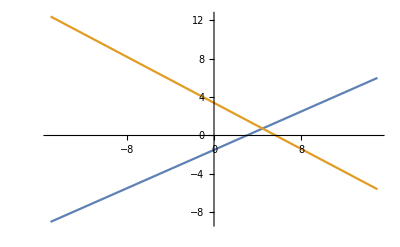

```mathematica
Plot[{x/2-3/2,17/5-3x/5},{x,-15,15}]
```

```mathematica
Solve[{x-2y==3,3x+5y==17},{x,y}]
```

{{x→49/11,y→8/11}}

Svar:
x=49/11
y=8/11

## 4-Problem 6

-Graphics-

```mathematica
Quit
```

För att lösa den ekvationen grafiskt måste rita den först.

```mathematica
ContourPlot3D[{3 x+4 y-z==8,6 x+8 y-2 z==3},{x,-10,10},{y,-10,10},{z,-10,10},PlotTheme->"Marketing"]
```

-Graphics3D-

Svar:
Från figuren visar att ekvationen saknar lösning

## 5-Problem 7

-Graphics-

```mathematica
Quit
```

Först är deklarera matriserna (A, B och C) sedan beräknar (A-B+C) , (ABC) och (CBA)

```mathematica
MatrixA={{3,2,4},{7,12,0},{2,5,2}}
```

{{3,2,4},{7,12,0},{2,5,2}}

```mathematica
MatrixB={{5,8,7},{6,4,9},{10,1,0}}
```

{{5,8,7},{6,4,9},{10,1,0}}

```mathematica
MatrixC = {{5,22,5},{5,9,7},{6,8,2}}
```

{{5,22,5},{5,9,7},{6,8,2}}

```mathematica
ABC=MatrixA-MatrixB + MatrixC
```

{{3,16,2},{6,17,-2},{-2,12,4}}

```mathematica
MatrixForm[{{3,16,2},{6,17,-2},{-2,12,4}}]
```

(3 | 16 | 2
6 | 17 | -2
-2 | 12 | 4)

```mathematica
ABC= Dot[MatrixA,MatrixB,MatrixC]
```

{{749,2110,665},{1997,4546,1577},{844,2134,684}}

```mathematica
MatrixForm[{{749,2110,665},{1997,4546,1577},{844,2134,684}}]
```

(749 | 2110 | 665
1997 | 4546 | 1577
844 | 2134 | 684)

```mathematica
CBA=Dot[MatrixC,MatrixB,MatrixA]
```

{{2018,3175,1294},{1260,1874,828},{1096,1750,620}}

```mathematica
MatrixForm[{{2018,3175,1294},{1260,1874,828},{1096,1750,620}}]
```

(2018 | 3175 | 1294
1260 | 1874 | 828
1096 | 1750 | 620)

Svar:
Jag fick (A-B+C) , (ABC) och (CBA)

## 6-Problem 8

-Graphics-

```mathematica
Quit
```

Först börjar med deklarera matrisen sedan radreducera.

```mathematica
MatrixA={{2,4,8},{4,5,1},{7,9,3}}
```

{{2,4,8},{4,5,1},{7,9,3}}

```mathematica
RowReduce[MatrixA]
```

{{1,0,-6},{0,1,5},{0,0,0}}

```mathematica
MatrixForm[{{1,0,-6},{0,1,5},{0,0,0}}]
```

(1 | 0 | -6
0 | 1 | 5
0 | 0 | 0)

Svar: är övan

## 7-Problem 9

-Graphics-

```mathematica
Quit
```

För hitta egenvärdena först måsta vi deklarera matrisen. Med hjälp av (A-λΙ) hittar vi determinant och λ_1,λ_2,λ_3 och λ_4

```mathematica
MatrixA={{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}}
```

{{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}}

```mathematica
MatrixForm[{{9,-4,-2,-4},{-56,32,-28,44},{-14,-14,6,-14},{42,-33,21,-45}}]
```

(9 | -4 | -2 | -4
-56 | 32 | -28 | 44
-14 | -14 | 6 | -14
42 | -33 | 21 | -45)

```mathematica
Eigenvalues[MatrixA]
```

{13,13,-12,-12}

Svar:

Egenvärden för λ_1,λ_2,λ_3 och λ_4 är {13,13,-12,-12}

## 8-Problem 15

-Graphics-

```mathematica
Quit
```

Först är börja med deklarera matrisen

```mathematica
MatrisA = {{5,-3,4,2},{9,1,8,-6},{6,-2,5,0},{0,0,1,0}};
```

```mathematica
MatrisA//MatrixForm
```

(5 | -3 | 4 | 2
9 | 1 | 8 | -6
6 | -2 | 5 | 0
0 | 0 | 1 | 0)

```mathematica
Det[MatrisA]
```

0

Eftersom determinanten är = 0 då är linjärt broende och det innebär att de kan utgöra en bas för vektorrummet.

## 9-Problem 18

-Graphics-

```mathematica
Quit
```

Först börja med att deklarera matrisen A sedan vi börja med att hitta determinat till (A-λΙ) sedan diagonal matris D och få P-Matrisen och P-InversMatrisen

```mathematica
MatrixA=MatrixForm[{{-6,4,0,9},{-3,0,1,6},{-1,-2,1,0},{-4,4,0,7}}]
```

(-6 | 4 | 0 | 9
-3 | 0 | 1 | 6
-1 | -2 | 1 | 0
-4 | 4 | 0 | 7)

```mathematica
Eigenvalues[MatrixA]
```

```mathematica
Eigenvalues[({{-6, 4, 0, 9}, {-3, 0, 1, 6}, {-1, -2, 1, 0}, {-4, 4, 0, 7}})]
```

{5,-2,-2,1}

```mathematica
MatrixD=MatrixForm[DiagonalMatrix[{5,-2,-2,1}]]
```

(5 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | 1)

```mathematica
MatrisP=Transpose [Eigenvectors[({{-6, 4, 0, 9}, {-3, 0, 1, 6}, {-1, -2, 1, 0}, {-4, 4, 0, 7}})]]
```

```mathematica
{{2,6,1,2},{1,-3,1,-1},{-1,0,1,-7},{2,4,0,2}}
```

```mathematica
MatrixForm[MatrisP]
```

(2 | 6 | 1 | 2
1 | -3 | 1 | -1
-1 | 0 | 1 | -7
2 | 4 | 0 | 2)

```mathematica
MatrisPInvaers=Inverse[MatrisP];
```

```mathematica
MatrixForm[MatrisPInvaers]
```

(-5/14 | 2/7 | 1/14 | 3/4
2/21 | -1/7 | 1/21 | 0
17/21 | 2/7 | -2/21 | -1
1/6 | 0 | -1/6 | -1/4)

Svar:
Jag fick fram D-Matris och P-Matris samt P^-1-Matris

## 10-Problem 19

19. Lös uppgift 34 i kapitel 6.1 i Lay, Sida 355.

-Graphics-

```mathematica
Quit
```

Först börjar med att deklarera matrisen A  sedan vi behöver hitta matris N och R

```mathematica
MatrisA=MatrixForm[{{-6,3,-27,-33,-13},{6,-5,25,28,14},{8,-6,34,38,18},{12,-10,50,41,23},{14,-21,49,29,33}}]
```

(-6 | 3 | -27 | -33 | -13
6 | -5 | 25 | 28 | 14
8 | -6 | 34 | 38 | 18
12 | -10 | 50 | 41 | 23
14 | -21 | 49 | 29 | 33)

```mathematica
RadreducerA=RowReduce[MatrisA]
```

```mathematica
RowReduce[({{-6, 3, -27, -33, -13}, {6, -5, 25, 28, 14}, {8, -6, 34, 38, 18}, {12, -10, 50, 41, 23}, {14, -21, 49, 29, 33}})]
```

{{1,0,5,0,-1/3},{0,1,1,0,-4/3},{0,0,0,1,1/3},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
MatrisR=MatrixForm[{{1,0,5,0,-1/3},{0,1,1,0,-4/3},{0,0,0,1,1/3},{0,0,0,0,0},{0,0,0,0,0}}]
```

(1 | 0 | 5 | 0 | -1/3
0 | 1 | 1 | 0 | -4/3
0 | 0 | 0 | 1 | 1/3
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
MatrixR=MatrixForm[{{1,0,5,0,-1/3},{0,1,1,0,-4/3},{0,0,0,1,1/3}}]
```

(1 | 0 | 5 | 0 | -1/3
0 | 1 | 1 | 0 | -4/3
0 | 0 | 0 | 1 | 1/3)

```mathematica
matrisN=MatrixForm[{{-5,1},{-1,4},{1,0},{0,-1},{0,3}}]
```

(-5 | 1
-1 | 4
1 | 0
0 | -1
0 | 3)

```mathematica
MatrixR.matrisN
```

```mathematica
({{1, 0, 5, 0, -1/3}, {0, 1, 1, 0, -4/3}, {0, 0, 0, 1, 1/3}}).({{-5, 1}, {-1, 4}, {1, 0}, {0, -1}, {0, 3}})
```

{{0,0},{0,0},{0,0}}

Svar:
Jag fick fram Matris R och N matris enligt Theorem 3. Samt att få fram noll-matrisen när är R*N.